CSE 477 G. Farin
HW 1, due 2/7, midnight

Degree elevation and reduction

Let a Bezier control polygon be given by

```mathematica
bb = Table[{i^1.5,Sqrt[i]},{i,1,6}];
```

1. Degree elevate to degree 15.
2. Add noise to the obtained control points.
3. Degree reduce to degree 5.

For graduate students: analyze the error between original curve and the curve from 3. Base this on the effect of different noise levels.

## Work

```mathematica
pts = Table[{i^1.5, Sqrt[i], 0}, {i, 1, 6}]
```

{{1.,1,0},{2.82843,√2,0},{5.19615,√3,0},{8.,2,0},{11.1803,√5,0},{14.6969,√6,0}}

```mathematica
graph1 =  Graphics3D[{BezierCurve[pts], Green, Line[pts], Red, Point[pts]}]
```

-Graphics3D-

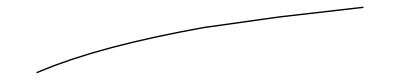

```mathematica
graph2 = Graphics[{BezierCurve[pts]}]
```